Convergence Issues for Gaussian wells.

1.) For plane waves, want to see convergence in both system size (L) and maximum k.  (specifying a L and k_max is probably the best way to parameterize this).  Do this for: (i) 1 well and (ii) 2 well.

i)

```mathematica
computePlaneMatrix[V_,c_,length_,p_]:= Module[{l,m,H,Em,M,norm},
(*First normalize the plane wave on the length*)
H[l_,m_]:=m^2/2 KroneckerDelta[m,l] - V*Exp[-(l-m)^2 c^2/2]*Sqrt[π]*c/(Sqrt[2]*length);
M = Eigensystem[Table[H[π*l/length,π*m/length],{l,-p/2.,p/2},{m,-p/2.,p/2.}]-10000*IdentityMatrix[p+1],1]

]
```

```mathematica
groundPlaneWave[EigenVec_,length_,p_,x_]:= Module[{Em,M,k},
Sum[k,{k,Table[Exp[-ⅈ*π*(n-p/2.)/length*x]/Sqrt[2*length]*Normalize[EigenVec][[n+1]], {n,0,p}]}]
]
```

```mathematica
ConvergenceLK = Table[{length,p,computePlaneMatrix[1.5,.5,length,p][[1]][[1]]+10000},{length ,.5,3},{p,1,30}];
```

```mathematica
PlaneMatrix = computePlaneMatrix[1.5,2.5,10,30
```

```mathematica
PlotData = Flatten[ConvergenceLK,1];
```

```mathematica
PlotData
```

{11.5,10,-10001.3}

```mathematica
p1 = ListPlot3D[PlotData,AxesLabel->{"length","Precision","E"}]
```

-Graphics3D-

```mathematica
p2 = ListPointPlot3D[Flatten[Table[{length,p,-0.6392504533509538},{length,.5,3,.1},{p,1,30}],1],PlotStyle->Black];
```

```mathematica
Show[p1,p2]
```

-Graphics3D-

The size of the gaussian in this case was c =2.5, so, as long as the length is 3*c, we seem to be able to converge.

```mathematica
EnergyConvergce1 = Eigensystem[HM[Sqrt[1.5/(.5)^2],1.5,0,.5,27]-100*IdentityMatrix[28],1][[1]][[1]]+100
```

-0.63925

```mathematica
EnergyConvergceNum = Eigensystem[computeMatrix[Ψp,Hp,9,1.5,2.5]-100*IdentityMatrix[10],1][[1]][[1]]+100
```

-1.27013

I was just double checking, to make sure that the energy really was 1.27. Calculated two different ways above.

ii) Two Wells

```mathematica
ConvergenceLK2Well = Table[{length,p,computePlaneMatrix2Well[1.5/2,2.5,5,length,p][[1]][[1]]+10000},{length ,.5,20},{p,1,30}];
```

```mathematica
PlotData2well = Flatten[ConvergenceLK2Well,1];
```

```mathematica
PlotData
```

{11.5,10,-10001.3}

```mathematica
computePlaneMatrix2Well[1.5/2,2.5,5,10,10][[1]][[1]]+10000
```

-0.596009

```mathematica
p3= ListPlot3D[PlotData2well,AxesLabel->{"length","Precision","E"}];
```

```mathematica
p4  = ListPointPlot3D[Flatten[Table[{length,p,-.594},{length,.5,20},{p,1,30}],1],PlotStyle->Black];
```

```mathematica
Show[p3,p4]
```

-Graphics3D-

```mathematica
Energy2WellANAL = Eigensystem[HM2Well[1.5/2,5,2.5,19]-IdentityMatrix[20]*10000,1][[1]][[1]]+10000
```

-0.594036

```mathematica
Energy2WellNum=Eigensystem[computeMatrix2Well[Ψp2wellnum,Hp2Well,14,1.5/2,5,2.5]-IdentityMatrix[15]*100,1][[1]][[1]]+100
```

-0.593973

#### 2) For harmonic oscillator, check convergence as a function of the interwell separation. (I expect it to converge slower as the distance becomes greater) d

```mathematica
Converg[b_]:= Module[{e1,e2,ϵ,n,counter},
e1=1; e2=10;n=20; counter=0;
While[n<50,
e1=e2;
e2=Eigensystem[HM2Well[1.5/2,b,.5,n]-IdentityMatrix[n+1]*10000,1][[1]][[1]]+10000;
ϵ=e2-e1;
(*Print[ϵ," , ",n];*)
If[Abs[ϵ]<.00001, counter = counter+1];
If[Abs[ϵ]>.00001,counter = 0];
(*Print["counter, ",counter,"  ,  ",n];*)
If[counter >6, Break[]];
n++];
n]
```

```mathematica
ConvergenceDistance = Table[{c,Converg[c]}, {c,.5,.5}]
```

$Aborted

$Aborted

{{0,27},{10,27},{20,36},{30,50},{40,50},{50,27},{60,27},{70,27},{80,27},{90,27},{100,27}}

This is interesting. Above, the convergence seems to start converging at 20 basis states, as b increases, that number quickly rises to
the cut-out (50), at around 30. However, after b=50, we drop back down to 20 basis states. This merits further investigation.

```mathematica
e2=Eigensystem[HM2Well[1.5/2,50,2.5,21]-IdentityMatrix[21+1]*10000,1][[1]][[1]]+10000
```

0.00118271

```mathematica
e1=Eigensystem[HM2Well[1.5/2,50,2.5,26]-IdentityMatrix[26+1]*10000,1][[1]][[1]]+10000
```

0.00093366

It seems like I was just not taking enough of a epsilon. There is an interesting convergence ‘kink’ around here, where it starts converging more slowly around b=30. Let’s see what these basis functions looks like at b=50.

```mathematica
Plot2Well[size_,b_]:= Module[{M},
M = Eigensystem[HM2Well[1.5/2,b,2.5,size]-1000*IdentityMatrix[size+1]];

{Plot[Sum[Ψp2wellnum[k,x,1.5/2,b,2.5]*Normalize[M[[2]][[1]]][[k+1]],{k,0,size}],{x,-b-10,b+10},PlotRange->{-.5,.5}],M[[1]][[1]]+1000}
]
```

```mathematica
Plot2WellExcited[size_,b_]:= Module[{M},
M = Eigensystem[HM2Well[1.5/2,b,2.5,size]-1000*IdentityMatrix[size+1]];

{Plot[Sum[Ψp2wellnum[k,x,1.5/2,b,2.5]*Normalize[M[[2]][[2]]][[k+1]],{k,0,size}],{x,-b-10,b+10},PlotRange->{-.5,.5}],M[[1]][[2]]+1000}
]
```

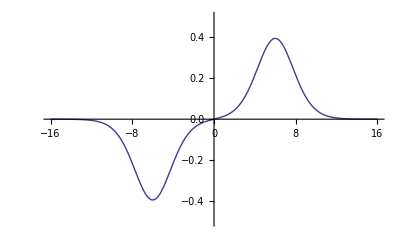
{-Graphics-,-0.591909}

```mathematica
p5 = Plot2WellExcited[30,6]
```

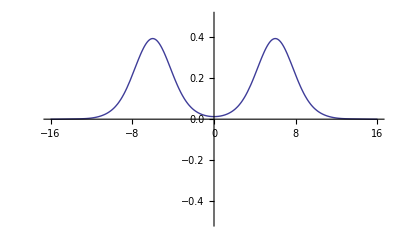
{-Graphics-,-0.592063}

```mathematica
p5 = Plot2Well[20,6]
```

```mathematica
(M2well = computePlaneMatrix2Well[1.5/2,2.5,6,30,200]);
```

```mathematica
M2well[[1]][[1]]+10000
```

-0.59207

```mathematica
p8=Plot[Im[groundPlaneWave[M2well[[2]][[2]],30,200,x]],{x,-15,15},PlotRange->{-.5,.5},PlotStyle->Red];
```

```mathematica
p9=Plot[Re[groundPlaneWave[M2well[[2]][[1]],30,200,x]],{x,-15,15},PlotRange->{0,.5}];
```

```mathematica
p10=Plot[Re[groundPlaneWave[M2well[[2]][[3]],30,200,x]],{x,-15,15},PlotRange->{0,.5}];
```

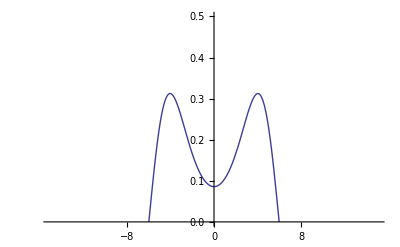

```mathematica
Show[p10]
```

```mathematica
groundPlaneWave[M2well[[2]][[1]],30,200,2]
```

0.0462849-9.841×10^-10 ⅈ

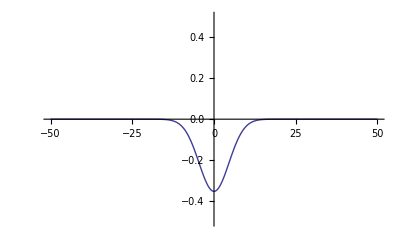
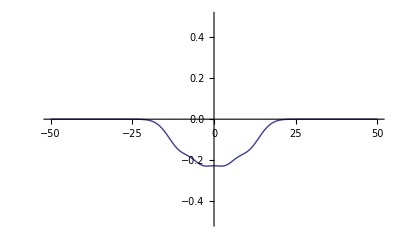
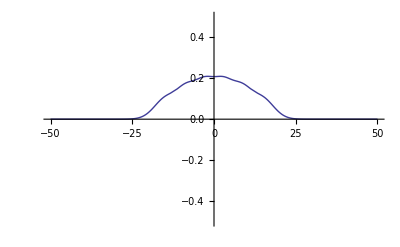
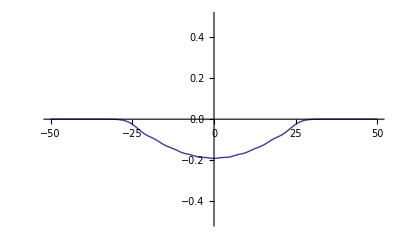
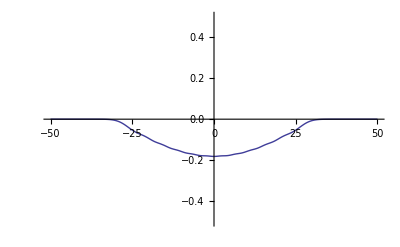
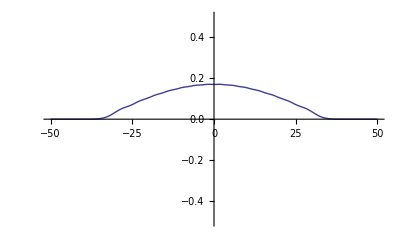
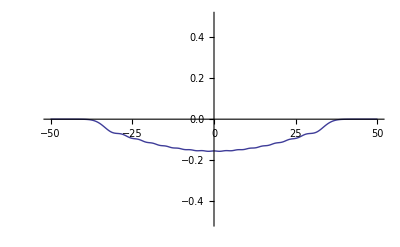
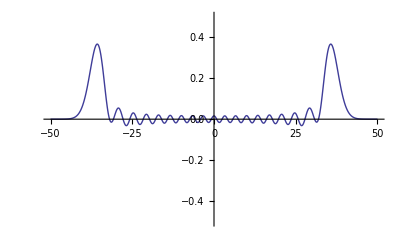

```mathematica
PlotTableBasisSize = Table[Plot2Well[i,40],{i,1,50,5}]
```

I thought it would be interesting to see the ‘mitosis’ of the ground state as the basis is increased. It gives a qualitative look at the convergenece.

Quantiative Convegence:

```mathematica
Energy2WellANAL = Eigensystem[HM2Well[1.5/2,.5,.5,30]-IdentityMatrix[31]*10000,1][[1]][[1]]+10000
```

-0.503016

```mathematica
Energy2WellNum=Eigensystem[computeMatrix2Well[Ψp2wellnum,Hp2Well,19,1.5/2,5,2.5]-IdentityMatrix[20]*100,1][[1]][[1]]+100
```

-0.594036

So, I am taking the value -.5940 to be the real energy. Now, I want to see how the energy difference scales for the plane wave basis.

computePlaneMatrix2Well[1.5/2,2.5,6,30,p][[1]][[1]] computePlaneMatrix2Well[V_,c_,b_,length_,p_]

```mathematica
Eigensystem[HM2Well[1.5/2,b,.5,n]-IdentityMatrix[n+1]*10000,1][[1]][[1]]+10000;
```

```mathematica
data = Table[{1/p,computePlaneMatrix2Well[1.5/2,.5,.5,10,p][[1]][[1]]},{p,1,100}];
```

Eigensystem::take: Cannot take eigenvectors and eigenvalues 1 through 3 out of the total of 2 eigenvectors and eigenvalues.

```mathematica
data[[40]][[2]]+10000
```

-0.503129

{{1,-0.232774},{1/2,-0.41932},{1/3,-0.41932},{1/4,-0.46495},{1/5,-0.46495},{1/6,-0.484544},{1/7,-0.484544},{1/8,-0.492923},{1/9,-0.492923},{1/10,-0.497239},{1/11,-0.497239},{1/12,-0.499555},{1/13,-0.499555},{1/14,-0.500884},{1/15,-0.500884},{1/16,-0.501678},{1/17,-0.501678},{1/18,-0.502169},{1/19,-0.502169},{1/20,-0.50248},{1/21,-0.50248},{1/22,-0.502683},{1/23,-0.502683},{1/24,-0.502818},{1/25,-0.502818},{1/26,-0.50291},{1/27,-0.50291},{1/28,-0.502972},{1/29,-0.502972},{1/30,-0.503016},{1/31,-0.503016},{1/32,-0.503047},{1/33,-0.503047},{1/34,-0.503069},{1/35,-0.503069},{1/36,-0.503084},{1/37,-0.503084},{1/38,-0.503096},{1/39,-0.503096},{1/40,-0.503104}}

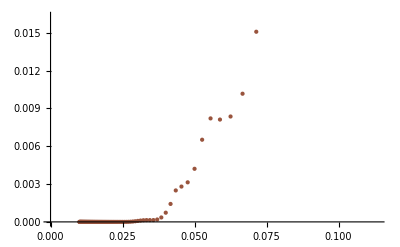

```mathematica
data1 = Table[{1/p,Eigensystem[HM2Well[1.5/2,.5,.5,p]-IdentityMatrix[p+1]*10000,1][[1]][[1]]+10000},{p,1,40}]
```

```mathematica
LogData= Table[{p,Log[Abs[data[[p+1]][[2]]-data[[p]][[2]]]]},{p,1,99}];
```

```mathematica
LogData= Table[{p,Log[Abs[data1[[p+1]][[2]]-data1[[p]][[2]]]]},{p,1,39}];
```

```mathematica
MixData = Table[{p,Log[Abs[data[[p]][[2]]-data1[[p]][[2]]+10000]]},{p,1,40}]
```

{{1,{-1.88973,9.21035}},{2,-1.73423},{3,-2.13963},{4,-2.16478},{5,-2.58062},{6,-2.73851},{7,-3.19083},{8,-3.44723},{9,-3.97339},{10,-4.28884},{11,-4.95245},{12,-5.34493},{13,-6.40494},{14,-6.98328},{15,-7.85555},{16,-7.81032},{17,-7.02939},{18,-7.31733},{19,-7.12576},{20,-7.49077},{21,-7.44452},{22,-7.8509},{23,-7.84905},{24,-8.27445},{25,-8.26976},{26,-8.69006},{27,-8.66061},{28,-9.05544},{29,-9.00121},{30,-9.3612},{31,-9.29584},{32,-9.62416},{33,-9.56214},{34,-9.86742},{35,-9.81699},{36,-10.1075},{37,-10.0707},{38,-10.3519},{39,-10.3274},{40,-10.6022}}

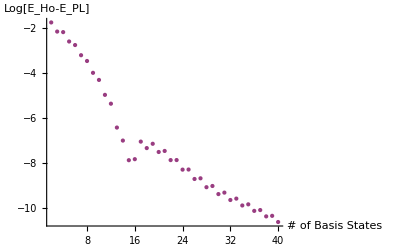

```mathematica
ListPlot[MixData,PlotRange->{0,-15},AxesLabel->{"# of Basis States","Log[E_Ho-E_PL]"}]
```

```mathematica
data[[2]][[2]]
```

-10000.2

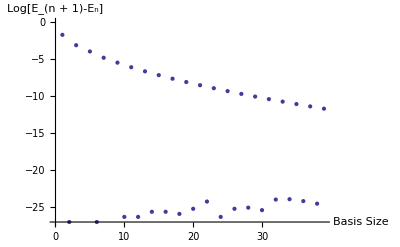

```mathematica
p11=ListPlot[LogData1,AxesLabel->{"Basis Size","Log[E_(n + 1)-E_n]"}]
```

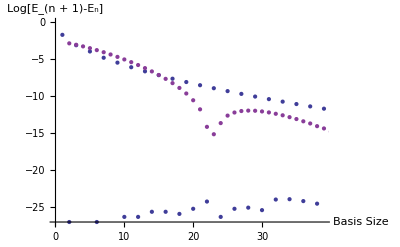

```mathematica
Show[p11,p13]
```

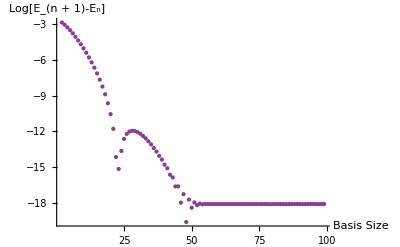

```mathematica
p13=ListPlot[LogData,AxesLabel->{"Basis Size","Log[E_(n + 1)-E_n]"},PlotRange->{0,-20}]
```

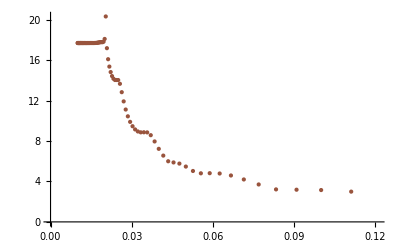

```mathematica
ListPlot[ Table[{1/p,Abs[Log[data[[p]][[2]]]]},{p,1,100}]]
```

```mathematica
computePlaneMatrix2Well[1.5/2,2.5,6,30,3][[1]][[1]]
```

-10000.4

Next step is to find the scaling behavior, it definitely looks exponential, with a sinusoid underneath. I will leave it like this for now.


Next is to look at how the tunneling scales with basis size:

Eigensystem[HM2Well[1.5/2,5,2.5,p]-IdentityMatrix[p+1]*10000,1][[1]][[2]]

```mathematica
TunnelingConverg = Table[{p, Eigensystem[HM2Well[1.5/2,1/4.,.5,p]-IdentityMatrix[p+1]*10000,2][[1]][[2]]-Eigensystem[HM2Well[1.5/2,1/4.,.5,p]-IdentityMatrix[p+1]*10000,2][[1]][[1]]},{p,1,25}]
```

{{1,1.62746},{2,1.73532},{3,1.2835},{4,1.32152},{5,1.10432},{6,1.11683},{7,1.00197},{8,1.00762},{9,0.934441},{10,0.937119},{11,0.886794},{12,0.888201},{13,0.851287},{14,0.85206},{15,0.823818},{16,0.824264},{17,0.801916},{18,0.802182},{19,0.784039},{20,0.784203},{21,0.769163},{22,0.769266},{23,0.756585},{24,0.756651},{25,0.745805}}

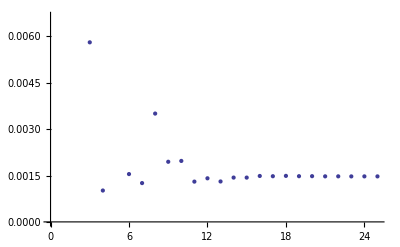

```mathematica
ListPlot[TunnelingConverg]
```

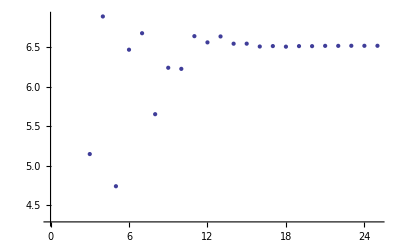

```mathematica
ListPlot[ Table[{p,Abs[Log[TunnelingConverg[[p]][[2]]]]},{p,1,25}]]
```

Try the plane wave now:

```mathematica
data = Table[{p,computePlaneMatrix2Well[1.5/2,2.5,5,30,p][[1]][[2]]-computePlaneMatrix2Well[1.5/2,2.5,5,30,p][[1]][[1]]},{p,1,100}]
```

Eigensystem::take: Cannot take eigenvectors and eigenvalues 1 through 3 out of the total of 2 eigenvectors and eigenvalues.

{{1,{10000.+0. ⅈ,-10000.+0. ⅈ}},{2,0.29324},{3,0.255874},{4,0.178251},{5,0.0908447},{6,0.0152518},{7,0.0373439},{8,0.0629242},{9,0.0628896},{10,0.0449977},{11,0.0204807},{12,0.00161005},{13,0.0163195},{14,0.0222679},{15,0.0208551},{16,0.0150886},{17,0.00812798},{18,0.00227054},{19,0.00136763},{20,0.00270901},{21,0.0023441},{22,0.00110279},{23,0.000285691},{24,0.00136623},{25,0.00197477},{26,0.0021587},{27,0.00206709},{28,0.0018589},{29,0.00165045},{30,0.00150097},{31,0.00142277},{32,0.001401},{33,0.0014119},{34,0.00143461},{35,0.00145596},{36,0.00147032},{37,0.00147729},{38,0.00147893},{39,0.00147777},{40,0.00147575},{41,0.00147397},{42,0.00147284},{43,0.00147231},{44,0.00147219},{45,0.00147226},{46,0.00147239},{47,0.0014725},{48,0.00147257},{49,0.0014726},{50,0.00147261},{51,0.0014726},{52,0.0014726},{53,0.00147259},{54,0.00147259},{55,0.00147259},{56,0.00147259},{57,0.00147259},{58,0.00147259},{59,0.00147259},{60,0.00147259},{61,0.00147259},{62,0.00147259},{63,0.00147259},{64,0.00147259},{65,0.00147259},{66,0.00147259},{67,0.00147259},{68,0.00147259},{69,0.00147259},{70,0.00147259},{71,0.00147259},{72,0.00147259},{73,0.00147259},{74,0.00147259},{75,0.00147259},{76,0.00147259},{77,0.00147259},{78,0.00147259},{79,0.00147259},{80,0.00147259},{81,0.00147259},{82,0.00147259},{83,0.00147259},{84,0.00147259},{85,0.00147259},{86,0.00147259},{87,0.00147259},{88,0.00147259},{89,0.00147259},{90,0.00147259},{91,0.00147259},{92,0.00147259},{93,0.00147259},{94,0.00147259},{95,0.00147259},{96,0.00147259},{97,0.00147259},{98,0.00147259},{99,0.00147259},{100,0.00147259}}

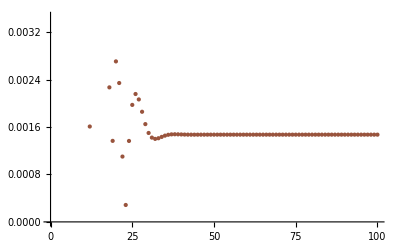

```mathematica
ListPlot[data]
```

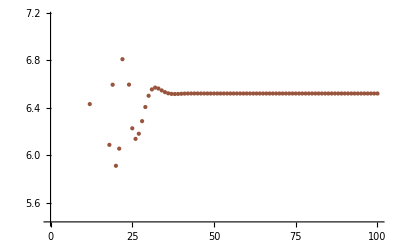

```mathematica
ListPlot[ Table[{p,Abs[Log[data[[p]][[2]]]]},{p,1,100}]]
```

## Timing of HO and Plane Wave Basis

```mathematica
TimeHO=Table[{n,Timing[Eigensystem[HM2Well[1.5/2,5,2.5,n]-IdentityMatrix[n+1]*10000,1][[1]][[1]]+10000][[1]]},{n,1,55}]
```

{{1,0.},{2,0.},{3,0.0156},{4,0.},{5,0.0156},{6,0.0156},{7,0.0312},{8,0.0312},{9,0.0312},{10,0.0624},{11,0.078},{12,0.078},{13,0.1092},{14,0.1248},{15,0.156},{16,0.1716},{17,0.2184},{18,0.234},{19,0.2652},{20,0.3276},{21,0.3432},{22,0.4056},{23,0.468},{24,0.5304},{25,0.5772},{26,0.6552},{27,0.7176},{28,0.79561},{29,0.88921},{30,0.982806},{31,1.07641},{32,1.24801},{33,1.29481},{34,1.43521},{35,1.54441},{36,1.66921},{37,1.80961},{38,1.93441},{39,2.13721},{40,2.32441},{41,2.46482},{42,2.65202},{43,2.90162},{44,3.10442},{45,3.29162},{46,3.49442},{47,3.75962},{48,3.99363},{49,4.30563},{50,4.61763},{51,4.94523},{52,5.33523},{53,5.55364},{54,5.92804},{55,6.24004}}

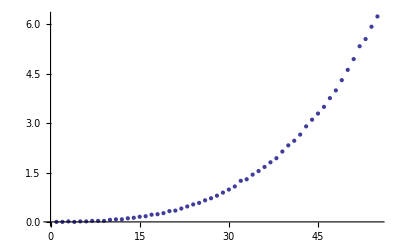

```mathematica
p11=ListPlot[TimeHO]
```

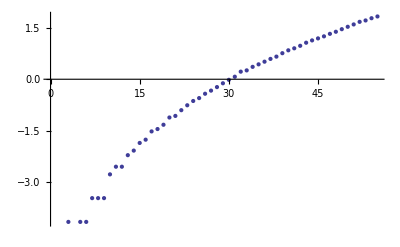

```mathematica
p13=ListPlot[ Table[{p,Log[TimeHO[[p]][[2]]]},{p,1,55}]]
```

```mathematica
TimePW = Table[{p,Timing[computePlaneMatrix2Well[1.5/2,2.5,5,30,p][[1]][[1]]+10000-Energy2WellANAL][[1]]},{p,1,100}]
```

Eigensystem::take: Cannot take eigenvectors and eigenvalues 1 through 3 out of the total of 2 eigenvectors and eigenvalues.

{{1,0.0624},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.0156},{7,0.},{8,0.0156},{9,0.0156},{10,0.0156},{11,0.0156},{12,0.0156},{13,0.0312},{14,0.0156},{15,0.0312},{16,0.0312},{17,0.0468},{18,0.0312},{19,0.0468},{20,0.0468},{21,0.0624},{22,0.0468},{23,0.078},{24,0.0624},{25,0.078},{26,0.078},{27,0.0936},{28,0.0936},{29,0.0936},{30,0.1092},{31,0.1092},{32,0.1248},{33,0.156},{34,0.1248},{35,0.1404},{36,0.156},{37,0.1716},{38,0.156},{39,0.1872},{40,0.2028},{41,0.1872},{42,0.234},{43,0.2184},{44,0.2184},{45,0.2496},{46,0.2496},{47,0.2652},{48,0.2808},{49,0.2964},{50,0.2964},{51,0.312},{52,0.3276},{53,0.3432},{54,0.3432},{55,0.3588},{56,0.3588},{57,0.39},{58,0.3744},{59,0.4056},{60,0.39},{61,0.4368},{62,0.4524},{63,0.468},{64,0.4836},{65,0.4992},{66,0.5148},{67,0.5304},{68,0.546},{69,0.5616},{70,0.5616},{71,0.6084},{72,0.624},{73,0.624},{74,0.6552},{75,0.6708},{76,0.6864},{77,0.6864},{78,0.702},{79,0.7488},{80,0.81121},{81,0.87361},{82,0.81121},{83,0.87361},{84,0.82681},{85,0.85801},{86,0.90481},{87,0.90481},{88,0.92041},{89,0.90481},{90,0.967206},{91,0.967206},{92,1.15441},{93,1.20121},{94,1.38841},{95,1.23241},{96,1.15441},{97,1.13881},{98,1.15441},{99,1.15441},{100,1.21681}}

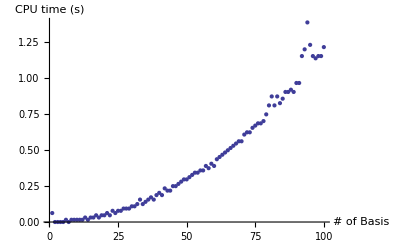

```mathematica
p12 = ListPlot[TimePW,AxesLabel->{"# of Basis","CPU time (s)"}]
```

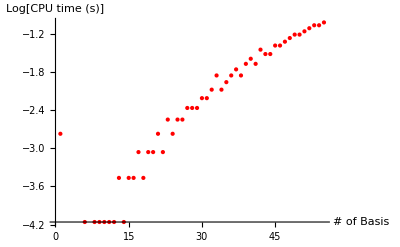

```mathematica
p14=ListPlot[ Table[{p,Log[TimePW[[p]][[2]]]},{p,1,55}],PlotStyle->Red,AxesLabel->{"# of Basis","Log[CPU time (s)]"}]
```

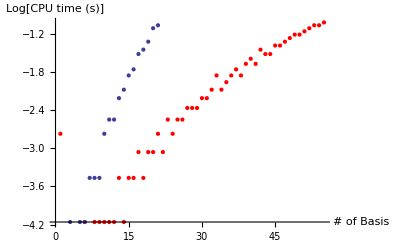

```mathematica
Show[p14,p13]
```

## Rey Group Talk

```mathematica
Em=Eigensystem[HM [Sqrt[1.5/(.5)^2],1.5,0,.5,30]-IdentityMatrix[31]*1000];
```

```mathematica
Dot[{1,2,4},{2,3,4}]
```

24

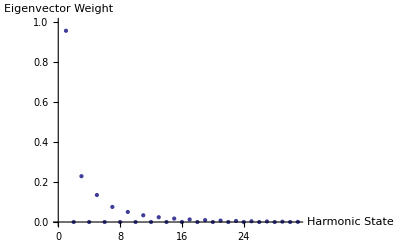

```mathematica
ListPlot[Table[{p,Abs[Normalize[Em[[2]][[1]]][[p]]]},{p,1,31}],PlotRange->{0,1},AxesLabel->{"Harmonic State","Eigenvector Weight"}]
```

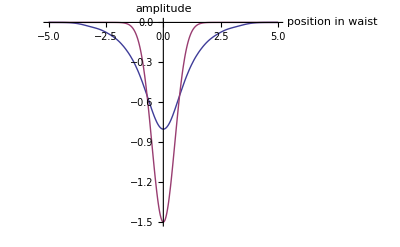

```mathematica
p1=Plot[{Sum[k,{k,Table[Ψp[n,x,1.5,.5]*Normalize[Em[[2]][[2]]][[n+1]], {n,0,18}]}],-1.5*Exp[-x^2*2]},{x,-5,5},PlotRange->{0,-1.5},AxesLabel->{"position in waist","amplitude"}]
```

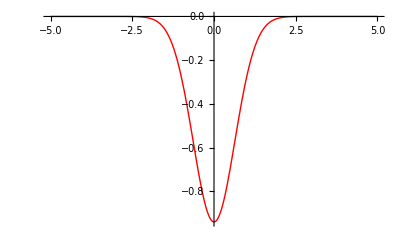

```mathematica
p2 = Plot[{-Ψp[1,x,1.5,.5]},{x,-5,5},PlotRange->{0,-1.5},PlotStyle->{Red}]
```

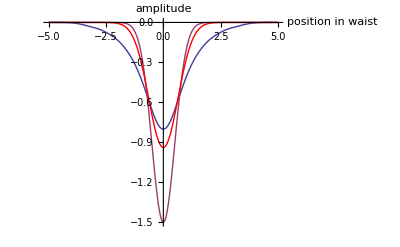

```mathematica
Show[p1,p2]
```

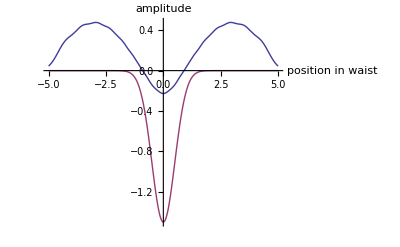

```mathematica
p20=Plot[{Sum[k,{k,Table[Ψp[n,x,1.5,.5]*Normalize[Em[[2]][[3]]][[n+1]], {n,0,30}]}],-1.5*Exp[-x^2*2]},{x,-5,5},PlotRange->{1.5,-1.5},AxesLabel->{"position in waist","amplitude"}]
```

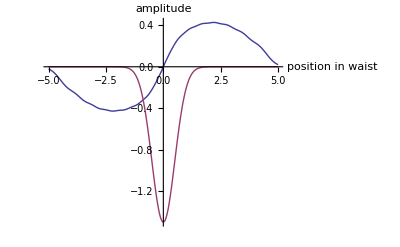

```mathematica
p3=Plot[{Sum[k,{k,Table[Ψp[n,x,1.5,.5]*Normalize[Em[[2]][[2]]][[n+1]], {n,0,30}]}],-1.5*Exp[-x^2*2]},{x,-5,5},PlotRange->{1.5,-1.5},AxesLabel->{"position in waist","amplitude"}]
```

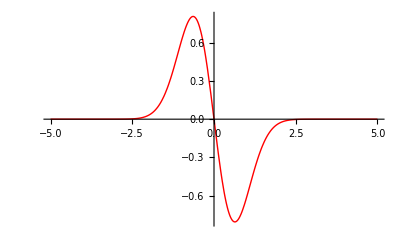

```mathematica
p4 = Plot[{-Ψp[1,x,1.5,.5]},{x,-5,5},PlotRange->{1.5,-1.5},PlotStyle->{Red}]
```

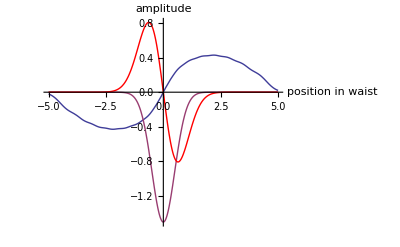

```mathematica
Show[p3,p4]
```

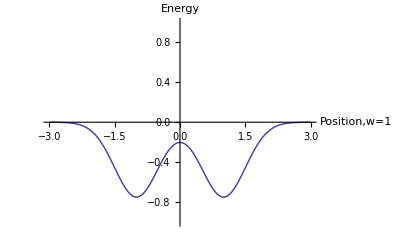

```mathematica
p1=Plot[{-1.5/2*Exp[-2*(x-1)^2]-1.5/2*Exp[-2*(x+1)^2]},{x,-3,3},AxesLabel->{"Position,w=1","Energy"},PlotRange->{-1,1}]
```

```mathematica
Table[n-10,{n,0,20}]
```

{-10,-9,-8,-7,-6,-5,-4,-3,-2,-1,0,1,2,3,4,5,6,7,8,9,10}

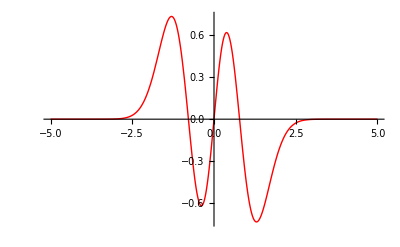

```mathematica
p21 = Plot[{-Ψp[3,x,1.5,.5]},{x,-5,5},PlotRange->{1.5,-1.5},PlotStyle->{Red}]
```

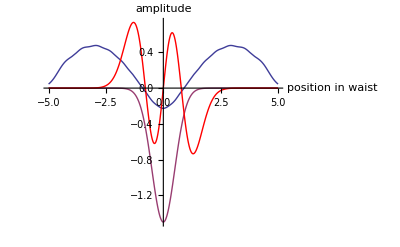

```mathematica
Show[p20,p21]
```

```mathematica
TunnelingInterwell = Table[{p, Eigensystem[HM2Well[1.5/2,p,.5,40]-IdentityMatrix[40+1]*10000,2][[1]][[2]]-Eigensystem[HM2Well[1.5/2,p,.5,40]-IdentityMatrix[40+1]*10000,2][[1]][[1]]},{p,.2,.5,.1}]
```

{{0.2,0.716855},{0.3,0.678107},{0.4,0.62972},{0.5,0.575734}}

```mathematica
TunnelingInterwellP=Table[{p,computePlaneMatrix2Well[1.5/2,.5,p,15,40][[1]][[2]]-computePlaneMatrix2Well[1.5/2,.5,p,15,40][[1]][[1]]},{p,.3,4,.2}]
```

{{0.3,0.609664},{0.5,0.533854},{0.7,0.446465},{0.9,0.35088},{1.1,0.268961},{1.3,0.203335},{1.5,0.152928},{1.7,0.115024},{1.9,0.0867673},{2.1,0.0657504},{2.3,0.0501231},{2.5,0.0385167},{2.7,0.0299368},{2.9,0.023667},{3.1,0.0191971},{3.3,0.0161706},{3.5,0.01435},{3.7,0.0135941},{3.9,0.0138445}}

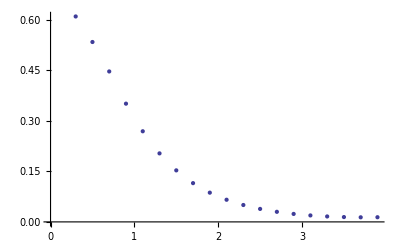

```mathematica
ListPlot[TunnelingInterwellP]
```

```mathematica
groundPlaneWave[computePlaneMatrix2Well[1.5/2,.5,2,15,40][[2]][[2]],15,40,0]
```

-0.0362506+0. ⅈ

```mathematica
Ground = computePlaneMatrix2Well[2,.5,1,10,40][[2]][[1]]
```

{2.56823×10^-7,4.56468×10^-7,2.55485×10^-7,-1.69553×10^-6,-8.04402×10^-6,-0.0000212273,-0.0000359021,-0.0000196446,0.000116386,0.000522458,0.00128517,0.00199404,0.000917292,-0.00572959,-0.0227643,-0.0504572,-0.0721598,-0.0378018,0.136974,0.477491,0.697854,0.477491,0.136974,-0.0378018,-0.0721598,-0.0504572,-0.0227643,-0.00572959,0.000917292,0.00199404,0.00128517,0.000522458,0.000116386,-0.0000196446,-0.0000359021,-0.0000212273,-8.04402×10^-6,-1.69553×10^-6,2.55485×10^-7,4.56468×10^-7,2.56823×10^-7}

```mathematica
Ground = computePlaneMatrix2Well[2,.5,1,10,20][[1]][[1]]+10000
```

-1.15427

```mathematica
computePlaneMatrix2WellT[2,.5,1,10,100][[1]][[1]]+10000
```

-1.15428

```mathematica
Clear[computePlaneMatrix2Well]
```

```mathematica
Ground2 = Eigensystem[HM2Well[2,1,.5,50]-100*IdentityMatrix[51]][[1]][[1]]+100
```

-1.15425

```mathematica
Excited =computePlaneMatrix2Well[2,.5,1,15,40][[2]][[2]]
```

{0.0000752296,0.000163636,0.000290481,0.000425166,0.000473022,0.000234607,-0.000623399,-0.00254401,-0.00593676,-0.0108404,-0.0163462,-0.0198289,-0.016198,0.00240776,0.0458176,0.122921,0.234874,0.360881,0.43337,0.329381,1.00395×10^-11,-0.329381,-0.43337,-0.360881,-0.234874,-0.122921,-0.0458176,-0.00240776,0.016198,0.0198289,0.0163462,0.0108404,0.00593676,0.00254401,0.000623399,-0.000234607,-0.000473022,-0.000425166,-0.000290481,-0.000163636,-0.0000752296}

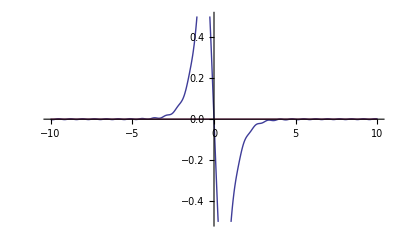

```mathematica
Plot[{Im[groundPlaneWave[Excited,15,40,x]],Re[groundPlaneWave[Excited,15,40,x]]},{x,-10,10},PlotRange->{-.5,.5}]
```

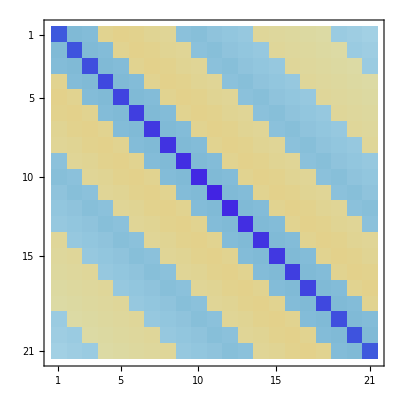

```mathematica
MatrixPlot[computePlaneMatrix2WellT[2,.5,1,10,20]]
```

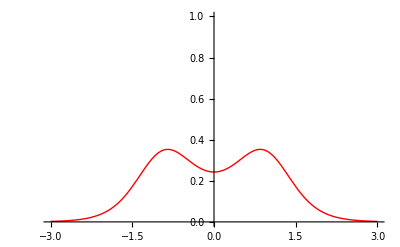

```mathematica
p2=Plot[{Abs[groundPlaneWave[Ground,10,40,x]]^2},{x,-3,3},PlotRange->{0,1},PlotStyle->Red]
```

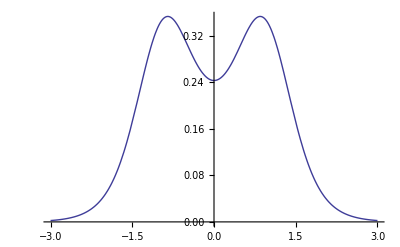

```mathematica
p4 = plotGround2wellHO[Ψp2wellnum,2,1,.5,50]
```

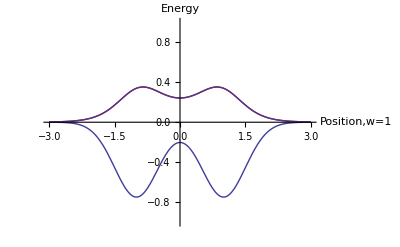

```mathematica
Show[p1,p2,p4]
```

```mathematica
dataWannierFunctionsG=Table[computePlaneMatrix2Well[2,.5,p,10,40][[2]][[1]],{p,.5,1.5,.1}]
```

```mathematica
dataWannierFunctionsE=Table[computePlaneMatrix2Well[2,.5,p,10,40][[2]][[2]],{p,.5,1.5,.1}];
```

```mathematica
Length[dataWannierFunctions]
```

11

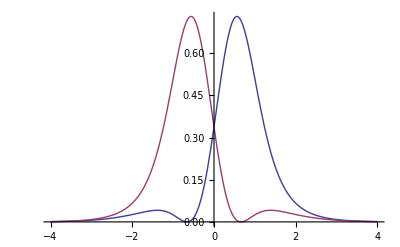
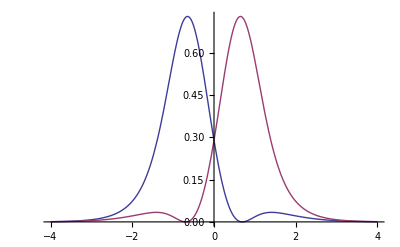
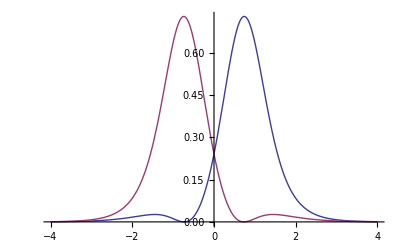
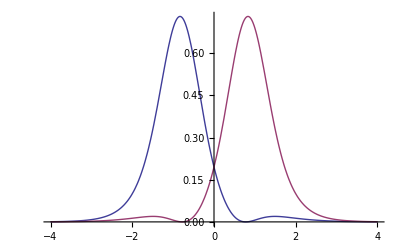
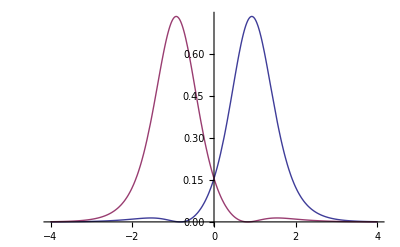
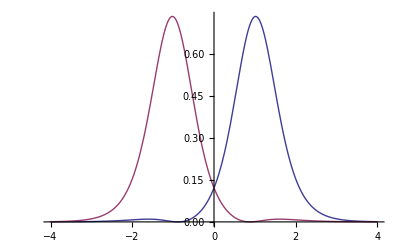
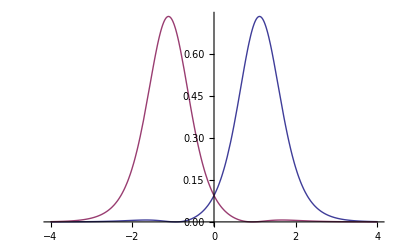
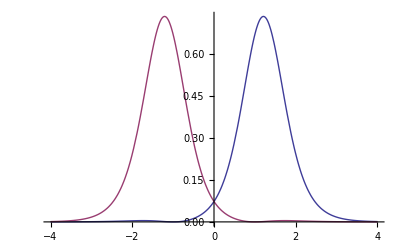

```mathematica
TunnelingStates = Table[Plot[{1/2 Abs[Re[groundPlaneWave[dataWannierFunctionsG[[p]],10,40,x]]+Im[groundPlaneWave[dataWannierFunctionsE[[p]],10,40,x]]]^2,1/2*Abs[Re[groundPlaneWave[dataWannierFunctionsG[[p]],10,40,x]]-Im[groundPlaneWave[dataWannierFunctionsE[[p]],10,40,x]]]^2},{x,-4,4}],{p,1,11}]
```

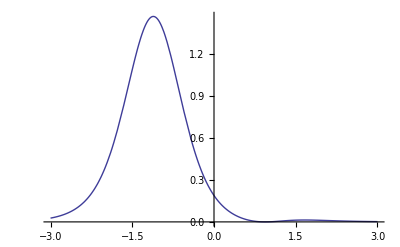

```mathematica
Plot[{Abs[Re[groundPlaneWave[dataWannierFunctionsG[[7]],10,40,x]]-Im[groundPlaneWave[dataWannierFunctionsE[[7]],10,40,x]]]^2},{x,-3,3}]
```

Part::partw: Part 5 of … does not exist.

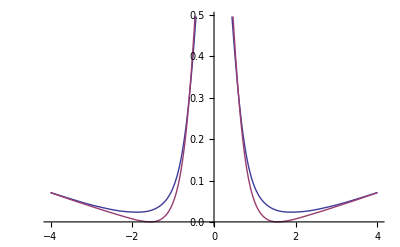
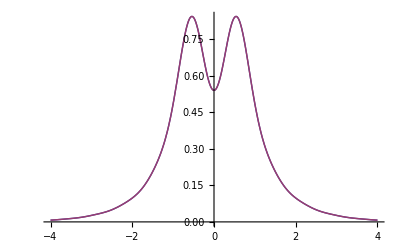
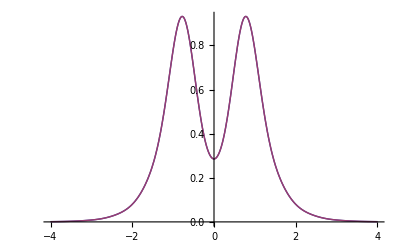
{-Graphics-,-Graphics-,-Graphics-}⟦5⟧

```mathematica
TunnelingStates[[]]
```

```mathematica
Converg2 = Table[{l,computePlaneMatrix[1.5,.5,l,16][[1]][[1]]+10000},{l,1,60,.5}];
```

```mathematica
E=computePlaneMatrix[1.5,.5,10,16][[1]][[1]]+10000
```

Set::wrsym: Symbol ⅇ is Protected.

-0.639273

```mathematica
Ground2 = Eigensystem[HM[Sqrt[1.5/(.5)^2],1.5,0,.5,50]-100*IdentityMatrix[51],1][[1]][[1]]+100
```

-0.639316

```mathematica
FourierTransform[Exp[-x^2/τ^2],x,(E1-E2)/h]
```

(ⅇ^(-(E1^2 τ^2)/(4 h^2)+(E1 E2 τ^2)/(2 h^2)-(E2^2 τ^2)/(4 h^2)))/(√2 √(1/τ^2))

```mathematica
60/12
```

```mathematica
Integrate[Exp[-x^2/(2*σ^2)-ⅈ*2*π*n/L*x],{x,-∞,∞}]
```

ConditionalExpression[(ⅇ^(-(2 n^2 π^2 σ^2)/L^2) √(2 π))/(√(1/σ^2)),Re[1/σ^2]>0]

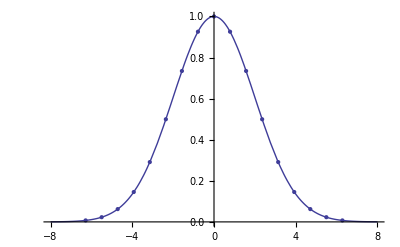
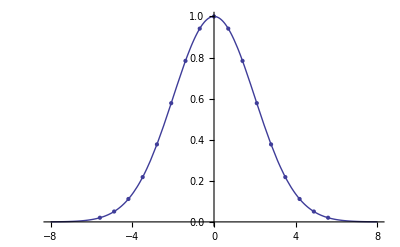
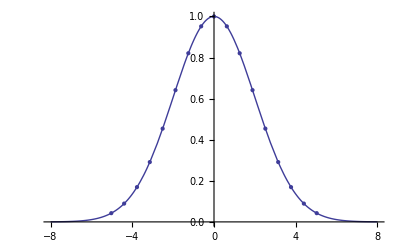
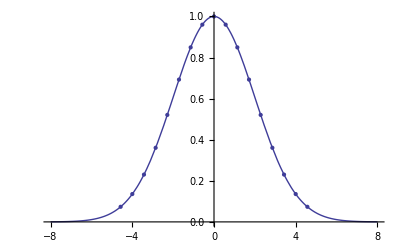
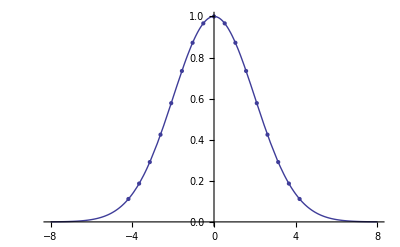
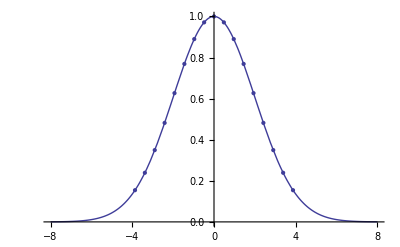
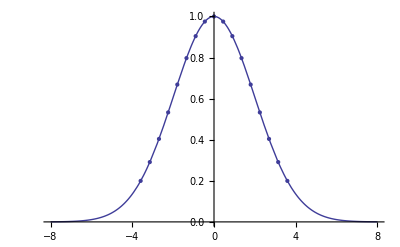
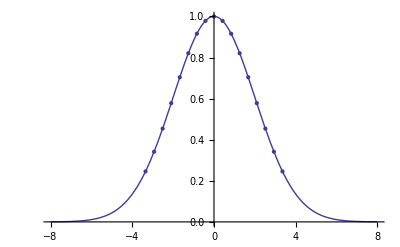

```mathematica
Table[Resolution[l,8],{l,8,15}]
```

```mathematica
Resolution[l_,p_] :=Module[{p1,p101,p100}, 
p1=Table[{(2*π/l)k,Exp[-(2 π/l)^2 k^2/8]},{k,-p,p}];
p101=Plot[Exp[-k^2/8],{k,-8,8},PlotRange->{0,1}];
p100=ListPlot[p1,PlotRange->{0,1}]; 
Show[p101,p100]]
```

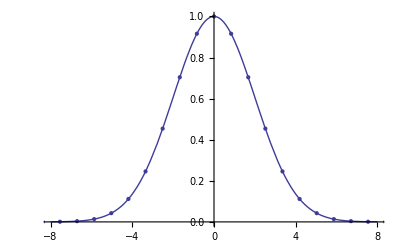

```mathematica
Resolution[7.5,20]
```

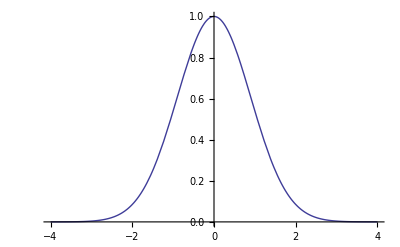

```mathematica
p101=Plot[Exp[-(2 π/8)^2 k^2],{k,-4,4}]
```

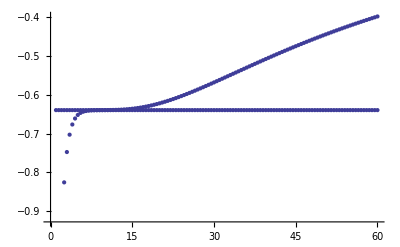

```mathematica
p10=ListPlot[Converg2];p11=ListPlot[Table[{l,Ground2},{l,1,60,.5}]];Show[p10,p11]
```

### FUNCTIONS

```mathematica
Φ[n_,x_] := 1/Sqrt[2^n Factorial[n]](m*ω/(π*h))^(1/4)*Exp[-m*ω*x^2/(2*h)]*HermiteH[n,Sqrt[m*ω/h]*x]
```

```mathematica
Ψp[n_,x_,V_,c_] := Φ[n,x]/.{ω->Sqrt[V/c^2],h->1,m->1}
```

```mathematica
Hp[x_,Φ_,V_,c_] := -1/2 D[D[Φ,x],x]-V*Exp[-x^2/(c^2*2)]Φ
```

```mathematica
computeMatrix[basis_, hamil_,size_,V_,c_]:=
				Module[{Ψ=basis, H=hamil, l = size},
	Table[NIntegrate[(Conjugate[Ψ[i,x,V,c]]H[x,Ψ[t,x,V,c],V,c]),{x,-∞,∞}],{i,0,l},{t,0,l}]//Chop//Quiet]
```

```mathematica
plotGround[Ψ_,H_,V_,c_,size_]:= Module[{Em,M,x,k},

(M=computeMatrix[Ψ,H,size,V,c]-1000*IdentityMatrix[size+1]);
(Em=Eigensystem[M])//MatrixForm;
Plot[{Sum[k,{k,Table[Ψ[n,x,V,c]*Normalize[Em[[2]][[1]]][[n+1]], {n,0,size}]}],-V/(c*Sqrt[2π])Exp[-x^2/(4*V*c^2)]},{x,-10,10}]
]
```

```mathematica
groundWave2[Ψ_,EigenVec_,V_,c_,x_,size_]:= Module[{Em,M,k},
Sum[k,{k,Table[Ψ[n-1,x,V,c]*Normalize[EigenVec[[1]]][[n]], {n,1,size}]}]
]
```

```mathematica
groundEn[Ψ_,H_,V_,c_,size_]:= Module[{Em,M,k},

(M=computeMatrix[Ψ,H,size,V,c]-1000.*IdentityMatrix[size+1]);

Em=Eigenvalues[M,1][[1]]+1000.
]
```

```mathematica
HMV1[l_,m_,ω_,b_,c_]:= (Sqrt[ω]/Sqrt[2^(l+m)Factorial[l]*Factorial[m]]*Sum[{2^k Factorial[k]*Binomial[l,k]*Binomial[m,k]*(1-2*(ω*c^2)/(1+2 c^2 ω))^((m+l)/2-k)*HermiteH[(m+l-2*k),Sqrt[ω/(1+2*c^2*ω)]*b]},{k,0,Min[m,l]}]*Exp[b^2/(2 c^2)(1/(1+2 c^2*ω)-1)]*Sqrt[2/(1+2 c^2*ω)]c)[[1]]
```

```mathematica
Hx2Anal2[l_,m_]:= 1/2(2*l+1)*KroneckerDelta[l,m]-1/2 Sqrt[(l+1)(l+2)]KroneckerDelta[l+1,m-1]-1/2 Sqrt[(m+1)(m+2)]KroneckerDelta[l-1,m+1]
```

```mathematica
HM [ω_,V_,b_,c_,size_]:= Table[ω/2*Hx2Anal2[n,m]-V*HMV1[n,m,ω,b,c],{n,0,size},{m,0,size}]
```

```mathematica
computePlaneMatrix[V_,c_,length_,p_]:= Module[{l,m,H,Em,M,norm},
(*First normalize the plane wave on the length*)
H[l_,m_]:=m^2/2 KroneckerDelta[m,l] - V*Exp[-(l-m)^2 c^2/2]*Sqrt[π]*(Sqrt[2]*c)/length;
M = Eigensystem[Table[H[2*π*l/length,2*π*m/length],{l,-p/2.,p/2},{m,-p/2.,p/2.}]-10000*IdentityMatrix[p+1],1]

]
```

```mathematica
groundPlaneWave[EigenVec_,length_,p_,x_]:= Module[{Em,M,k},
Sum[k,{k,Table[Exp[-ⅈ*2*π*(n-p/2.)/length*x]/Sqrt[length]*Normalize[EigenVec][[n+1]], {n,0,p}]}]
]
```

```mathematica
computePlaneMatrix2Well[V_,c_,b_,length_,p_]:= Module[{l,m,H,Em,M,norm},
(*First normalize the plane wave on the length*)
H[l_,m_]:=m^2/2 KroneckerDelta[m,l] - V*Exp[1/(2 c^2)(-b+ⅈ*c^2(l-m))^2-b^2/(2 c^2)]*Sqrt[π]*(Sqrt[2]c)/length-V*Exp[(1/(2 c^2)(b+ⅈ*c^2(l-m))^2-b^2/(2 c^2))]*Sqrt[π]*(Sqrt[2]c)/length;
M = Eigensystem[Table[H[2π*l/length,2π*m/length],{l,-p/2.,p/2},{m,-p/2.,p/2.}]-10000*IdentityMatrix[p+1],3]

]
```

```mathematica
HM2Well[V_,b_,c_,size_]:= Module[{ω=Sqrt[2*V/(6*b*c+9 c^2)]},
Table[ω/2*Hx2Anal2[n,m]-V*HMV1[n,m,ω,b,c]-V*HMV1[n,m,ω,-b,c],{n,0,size},{m,0,size}]
]
```

```mathematica
Ψp2wellnum[n_,x_,V_,b_,c_] := Φ[n,x]/.{ω->Sqrt[(2*V)/(6b*c+9 c^2)],h->1,m->1}
```

```mathematica
plotGround2wellHO[Ψ_,V_,b_,c_,size_]:= Module[{Em,M,x,k,ω=Sqrt[2*V/(6b*c+9 c^2)]},

(M=HM2Well[V,b,c,size]-1000*IdentityMatrix[size+1]);
(Em=Eigensystem[M])//MatrixForm;
Plot[{Abs[Sum[k,{k,Table[Ψ[n,x,V,b,c]*Normalize[Em[[2]][[1]]][[n+1]], {n,0,size}]}]]^2},{x,-3,3}]
]
```

```mathematica
Clear[Ψp2wellnum]
```

```mathematica
computePlaneMatrix2WellT[V_,c_,b_,length_,p_]:= Module[{l,m,H,Em,M,norm},
(*First normalize the plane wave on the length*)
H[l_,m_]:=m^2/2 KroneckerDelta[m,l] - V*Exp[1/(2 c^2)(-b+c^2 ⅈ(l-m))^2-b^2/(2 c^2)]*Sqrt[π]*(Sqrt[2]c)/length-V*Exp[1/(2 c^2)(b+c^2 ⅈ(l-m))^2-b^2/(2 c^2)]*Sqrt[π]*(Sqrt[2]c)/length;
M = Table[H[2*π*l/length,2*π*m/length],{l,-p/2.,p/2},{m,-p/2.,p/2.}]-10000*IdentityMatrix[p+1]

]
```

```mathematica
computePlaneMatrix2Well[V_,c_,b_,length_,p_]:= Module[{l,m,H,Em,M,norm},
(*First normalize the plane wave on the length*)
H[l_,m_]:=m^2/2 KroneckerDelta[m,l] - V*Exp[1/(2 c^2)(-b+ⅈ*c^2(l-m))^2-b^2/(2 c^2)]*Sqrt[π]*(Sqrt[2]c)/length-V*Exp[(1/(2 c^2)(b+ⅈ*c^2(l-m))^2-b^2/(2 c^2))]*Sqrt[π]*(Sqrt[2]c)/length;
M = Eigensystem[Table[H[2π*l/length,2π*m/length],{l,-p/2.,p/2},{m,-p/2.,p/2.}]-10000*IdentityMatrix[p+1],3]

]
```